```mathematica
Clear["Global`*"];
Off[NIntegrate::ncvb];
```

```mathematica
T0=0.5;(* ps *)
λ0=1.060;(* mkm *)
γ=5.5;(* 1/W *)
β2=-25.0; (* ps^2/km *)
CalcWindow=10;(* ps *)
N0=2^11-1;
L=0.002;(* km *)
h=0.000002;(* km *)
P=700;(* W *)
```

```mathematica
Frequency2Wavelength[λ0var_,CalcWindowvar_,N0var_]:=(LightSpeed=3×10^5;Return[ParallelTable[N[10^6 10^3(2 π LightSpeed)/(Δω+(2 π LightSpeed)/(λ0var×10^-6×10^-3))], {Δω, -π/(CalcWindowvar×10^-12)×(N0var-1)/2,π/(CalcWindowvar×10^-12)×(N0var-1)/2,π/(CalcWindowvar×10^-12)}]]);
```

```mathematica
WavelengthArray = Frequency2Wavelength[λ0,CalcWindow,N0];
TimeArray=ParallelTable[N[t],{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}];
```

```mathematica
PreGaussImp=ParallelTable[N[Exp[-(t^2(2 √(2Log[2]))^2)/(2 T0^2)]],{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}];
```

```mathematica
GaussImp=PreGaussImp×√P/√NIntegrate[Interpolation[Transpose[{Table[t,{t,-CalcWindow, +CalcWindow,(2 CalcWindow)/(N0-1)}],PreGaussImp^2}],InterpolationOrder->1][x],{x,-CalcWindow, +CalcWindow}];
```

```mathematica
(*{ListPlot[GaussImp,PlotRange->All,ImageSize->Medium],

ListPlot[RotateRight[Abs[Fourier[GaussImp]]^2,(N0-1)/2],PlotRange->{{1000,1050},Full},ImageSize->Medium],
ListPlot[RotateRight[Arg[Fourier[GaussImp]],(N0-1)/2],PlotRange->{{1000,1050},Full},ImageSize->Medium,Joined->True]};*)
```

```mathematica
SpatialOp[x_List]=Exp[I γ Abs[x]^2 h];
```

```mathematica
D2Fourier=Table[-((π k)/CalcWindow)^2,{k,0,N0/2}]~Join~Table[-((π(k-N0))/CalcWindow)^2,{k,Ceiling[N0/2],N0-1}];
FourierOp=Exp[-(I β2)/2 D2Fourier h];
```

```mathematica
Imp=GaussImp;
```

```mathematica
Imp=√FourierOp Fourier[Imp];
Monitor[
For[ξ=h/2,ξ<L,ξ+=h,
Imp=InverseFourier[Imp];
Imp*= SpatialOp[Imp];
Imp=FourierOp Fourier[Imp];
],Round[(1000 ξ)/L]×0.1]
Imp=InverseFourier[Imp/(√FourierOp)];
```

```mathematica
PulseIn=Transpose[{TimeArray,Abs[GaussImp]^2}];
PulseOut=Transpose[{TimeArray,Abs[Imp]^2}];
SpectrumIn=Transpose[{WavelengthArray,RotateLeft[Abs[Fourier[GaussImp]]^2,(N0-1)/2]}];
SpectrumOut=Transpose[{WavelengthArray,RotateLeft[Abs[Fourier[Imp]]^2,(N0-1)/2]}];
```

```mathematica
TempImp=RotateLeft[Fourier[Imp],(N0-1)/2];
ImpSpectrumSelected=RotateRight[Table[If[1.09<SpectrumOut[[i,1]]<1.11,TempImp[[i]],0],{i,1,N0}],(N0-1)/2];
ImpSelected=InverseFourier[ImpSpectrumSelected];
```

```mathematica
PulseSelected=Transpose[{TimeArray,Abs[ImpSelected]^2}];
SpectrumSelected=Transpose[{WavelengthArray,RotateLeft[Abs[Fourier[ImpSelected]]^2,(N0-1)/2]}];
```

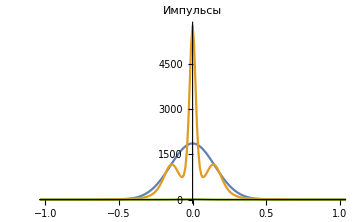
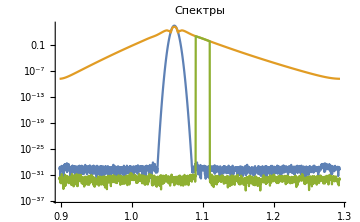
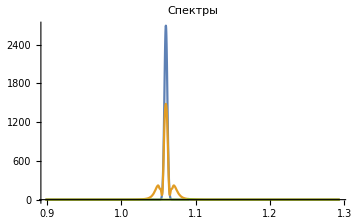

```mathematica
{ListPlot[{PulseIn,PulseOut,PulseSelected},PlotRange->{{-1,1},Full},Joined->True,ImageSize->Medium,PlotLabel->"Импульсы"],
ListLogPlot[{SpectrumIn,SpectrumOut,SpectrumSelected},PlotRange->{Full,Full},Joined->True,ImageSize->Medium,PlotLabel->"Спектры"],
ListPlot[{SpectrumIn,SpectrumOut,SpectrumSelected},PlotRange->{Full,Full},Joined->True,ImageSize->Medium,PlotLabel->"Спектры"](*,
ListPlot[{Arg[Fourier[GaussImp]],Arg[Fourier[Imp]]},PlotRange->{Full,Full},Joined->True,ImageSize->Medium,PlotLabel->"Фаза"]*)}
```

```mathematica
(*{ListPlot[Abs[Imp]^2,PlotRange->All,ImageSize->Medium],
ListPlot[RotateRight[Abs[Fourier[Imp]]^2,(N0-1)/2],PlotRange->{{1000,1050},Full},ImageSize->Medium],
ListPlot[RotateRight[Arg[Fourier[Imp]],(N0-1)/2],PlotRange->{{1000,1050},Full},ImageSize->Medium,Joined->True]};*)
```